EPToolbox package

## Initialization

This package includes a smal suite of supporting functions for varied applications. This file describes their usage.

To get things going, load the package.

```mathematica
Needs["EPToolbox`",NotebookDirectory[]<>"EPToolbox.m"]
```

The package can also be installed by adding $Path=Join[$Path,{“/path/to/EPToolbox”}] to the file ~/.Mathematica/Kernel/init.m.)

© Emilio Pisanty, 2014-2016, available under the CC-BY-SA 4.0 license.

## Functions

### FindComplexRoots

#### Description

This is a function to solve numerically (mainly trascendental) equations on the complex plane. It is documented in depth in http://mathematica.stackexchange.com/a/57821.

Its main usage is as follows:

```mathematica
?FindComplexRoots
Options[FindComplexRoots]
?Seeds
?SeedGenerator
?Tolerance
```

FindComplexRoots[e1==e2, {z, zmin, zmax}] attempts to find complex roots of the equation e1==e2 in the complex rectangle with corners zmin and zmax.

FindComplexRoots[{e1==e2, e3==e4, …}, {z1, z1min, z1max}, {z2, z2min, z2max}, …] attempts to find complex roots of the given system of equations in the multidimensional complex rectangle with corners z1min, z1max, z2min, z2max, ….

{AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision,Seeds→50,SeedGenerator→RandomComplex,Tolerance→Automatic,Verbose→False}

Seeds is an option for FindComplexRoots which determines how many initial seeds are used to attempt to find roots of the given equation.

SeedGenerator is an option for FindComplexRoots which determines the function   used to generate the seeds for the internal FindRoot call. Its value can be RandomComplex, RandomNiederreiterComplexes, RandomSobolComplexes, DeterministicComplexGrid, or any function f such that f[{zmin, zmax}, n] returns n complex numbers in the rectancle with corners zmin and zmax.

Tolerance is an option for various numerical options which specifies the tolerance that should be allowed in computing results.

#### Examples

```mathematica
FindComplexRoots[1+(1-Sin[t])^2==0.1 t, {t,-2ⅈ,2π+2ⅈ}]
```

{{t→2.46095+0.963404 ⅈ},{t→0.709879-1.06182 ⅈ},{t→2.46095-0.963404 ⅈ},{t→0.709879+1.06182 ⅈ}}

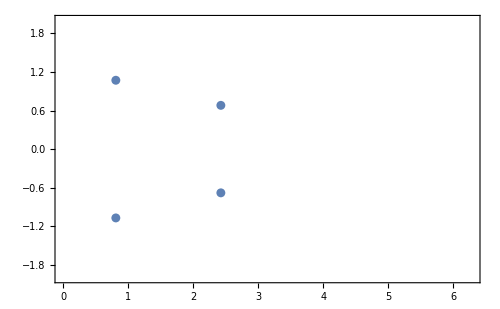

```mathematica
ListPlot[
{Re[t],Im[t]}/.FindComplexRoots[1+(1-Sin[t])^2== 0.3t, {t,-2ⅈ,2π+2ⅈ}]
,Frame->True
,ImageSize->500
,PlotRange->{{0,2 π},{-2,2}}
]
```

#### With multiple equations

```mathematica
(results=FindComplexRoots[
{1+(1-Sin[t])^2==0.001Sin[tt],1+(1+Sin[tt])^2==0.001Cos[t]}
, {t,-2ⅈ,2π+2ⅈ},{tt,0,2π+2ⅈ}
,SeedGenerator->RandomSobolComplexes
,Seeds->100
,Tolerance->0.01
])//Sort//Length
ListPointPlot3D[
Flatten[{ReIm[t],Re[tt]}]/.results
,ImageSize->450
,PlotRange->{{0,π},{-2,2},{π,2π}}
,PlotStyle->PointSize[Large]
]
```

8

-Graphics3D-

### Benchmarking suite for FindComplexRoots

FindComplexRoots works probabilistically, by randomly seeding points in the given rectangle and then using descent methods to find roots. This means that if not enough seeds are tried (i.e. the Seeds option is too low) then the function may behave erratically and return an incomplete (and varying) set of roots. To deal with this behaviour, the following is a benchmarking suite to help determine the seeding characteristics required by each equation for consistent behaviour.

#### Timings and generation of the benchmarks

```mathematica
Null
```

Null

#### Number of roots found vs number of seeds

Null

```mathematica
Null
```

Null

#### More detailed statistics on the distribution of roots found

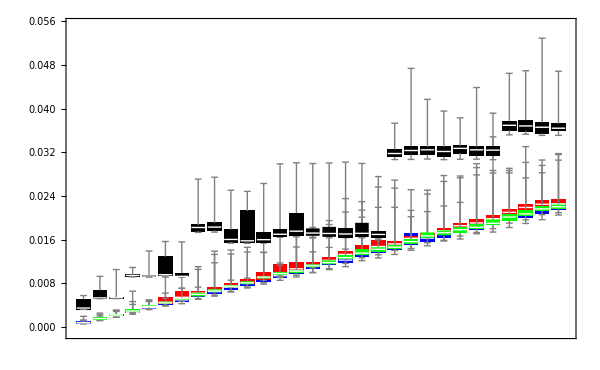

```mathematica
Null
```

### Quasirandom complex number generators.

#### Description

The performance of FindComplexRoots can be increased, as shown above, by using quasirandom numbers instead of pure random selections. (Pseudo)random numbers tend to bunch up, in the plane, which increases the chances of roots being missed or repeated. To remedy this, it is often beneficial to use low-discrepancy quasirandom number generators, which are more evenly distributed on the complex plane.

```mathematica
?RandomComplex
?RandomSobolComplexes
?RandomNiederreiterComplexes
?DeterministicComplexGrid
```

RowBox[{"RandomComplex", "[", "]"}] gives a pseudorandom complex number with real and imaginary parts in the range 0 to 1.
RowBox[{"RandomComplex", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["z", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["z", "TI"], StyleBox["max", "TI"]]}], "}"}], "]"}] gives a pseudorandom complex number in the rectangle with corners given by the complex numbers SubscriptBox[StyleBox["z", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["z", "TI"], StyleBox["max", "TI"]].
RowBox[{"RandomComplex", "[", SubscriptBox[StyleBox["z", "TI"], StyleBox["max", "TI"]], "]"}] gives a pseudorandom complex number in the rectangle whose corners are the origin and SubscriptBox[StyleBox["z", "TI"], StyleBox["max", "TI"]].
RowBox[{"RandomComplex", "[", RowBox[{StyleBox["range", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives a list of StyleBox["n", "TI"] pseudorandom complex numbers.
RowBox[{"RandomComplex", "[", RowBox[{StyleBox["range", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives an SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]]×SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]×… array of pseudorandom complex numbers.

RandomSobolComplexes[{zmin, zmax}, n] generates a low-discrepancy Sobol sequence of n quasirandom complex numbers in the rectangle with corners zmin and zmax.

RandomSobolComplexes[{{z1min,z1max},{z2min,z2max},…},n] generates a low-discrepancy Sobol sequence of n quasirandom complex numbers in the multi-dimensional rectangle with corners {z1min,z1max},{z2min,z2max},….

RandomNiederreiterComplexes[{zmin, zmax}, n] generates a low-discrepancy Niederreiter sequence of n quasirandom complex numbers in the rectangle with corners zmin and zmax.

RandomNiederreiterComplexes[{{z1min,z1max},{z2min,z2max},…},n] generates a low-discrepancy Niederreiter sequence of n quasirandom complex numbers in the multi-dimensional rectangle with corners {z1min,z1max},{z2min,z2max},….

DeterministicComplexGrid[{zmin, zmax}, n] generates a grid of about n equally spaced complex numbers in the rectangle with corners zmin and zmax.

DeterministicComplexGrid[{{z1min,z1max},{z2min,z2max},…},n] generates a regular grid of about n equally spaced complex numbers in the multi-dimensional rectangle with corners {z1min,z1max},{z2min,z2max},….

RandomComplex has also been modified to accept syntax of the form RandomComplex[{{z1min, z1max}, {z2min, z2max}, …}, n], for uniformity with the rest of the generators.

#### Distribution of the different (pseudo/quasi)random number generators on the complex plane

```mathematica
Null
```

Null

#### Timings statistics

```mathematica
Null
```

Null

### cleanContourPlot

Null

```mathematica
Null
```

Null

### profileDynamics

Null

```mathematica
Null
```